```mathematica
Clear["Global`*"]
```

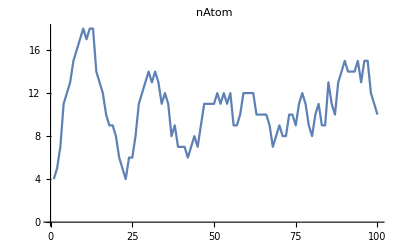

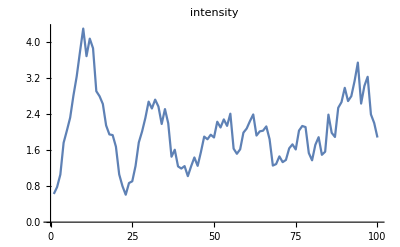

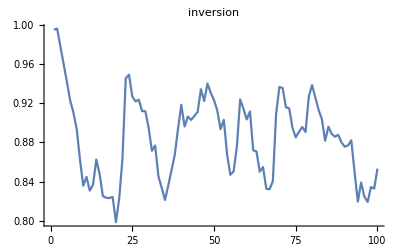

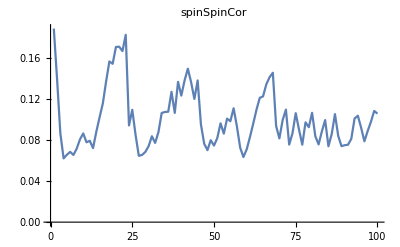

```mathematica
(*When doing one run*)
name ="test";
intensityy=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtomm=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionn=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
spinSpinCorr=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCor.dat"]];
ListLinePlot[nAtomm,PlotRange->All,PlotLabel->nAtom]
ListLinePlot[intensityy,PlotRange->All,PlotLabel->intensity]
ListLinePlot[inversionn,PlotRange->All,PlotLabel->inversion]
ListLinePlot[spinSpinCorr,PlotRange->All,PlotLabel->spinSpinCor]
```

```mathematica
intensityy
```

{0.624783,0.776817,1.0548,1.75953,2.02989,2.31514,2.80437,3.22938,3.77093,4.29089,3.67922,4.06768,3.85439,2.90262,2.79069,2.61877,2.1436,1.94489,1.9293,1.67297,1.05841,0.798398,0.607589,0.86668,0.905693,1.24461,1.76723,2.0092,2.30749,2.67117,2.51902,2.71565,2.56306,2.17615,2.50633,2.1904,1.45,1.6049,1.23566,1.18798,1.24195,1.01944,1.2373,1.43355,1.24737,1.5548,1.89589,1.83693,1.93776,1.87671,2.22568,2.09819,2.27752,2.13409,2.40367,1.62959,1.51511,1.61441,1.98393,2.07564,2.23967,2.38697,1.91947,2.0122,2.02748,2.12195,1.83859,1.25396,1.28701,1.45746,1.32984,1.37875,1.63592,1.72408,1.61101,2.02963,2.13164,2.10692,1.53184,1.3704,1.71401,1.8832,1.49238,1.56086,2.38324,1.97962,1.88794,2.5348,2.66064,2.97758,2.68394,2.79242,3.12738,3.53684,2.62827,3.01895,3.22236,2.38819,2.1972,1.87573}

```mathematica
L=Table[0,{i,20}];
```

```mathematica
For[i=0,i<20,i++,
x=Flatten[Import[NotebookDirectory[]<>"meanP"<>ToString[i]<>"/nAtom.dat"]];
x=Cases[x,Except[0|0.]];
L[[i+1]]=Last[x];
]
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

```mathematica
nAtomSS=Flatten[Import["/Users/westgatesnow/Desktop/Codes/2017/beamLaser/versusTau/nAtomSS.dat"]];
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
nAtomSS
```

Flatten[$Failed]

```mathematica
L
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
ListLinePlot[L]
```

-Graphics-

```mathematica
gc=1
```

1

```mathematica
Clear[gc,a]
```

```mathematica
a={{0,0.5gc,0,0,0.5gc,0},{0.5gc,0,0,0.5gc,0,0},{0,0,4gc,0,0,0},{0,0.5gc,0,0,0.5gc,0},{0.5gc,0,0,0.5gc,0,0},{0,0,0,0,0,4gc}}//MatrixForm
Eigenvalues[%]
```

(0 | 0.5 gc | 0 | 0 | 0.5 gc | 0
0.5 gc | 0 | 0 | 0.5 gc | 0 | 0
0 | 0 | 4 gc | 0 | 0 | 0
0 | 0.5 gc | 0 | 0 | 0.5 gc | 0
0.5 gc | 0 | 0 | 0.5 gc | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 gc)

{4. gc,4. gc,-1. gc,1. gc,-1.67735×10^-17 gc,1.67735×10^-17 gc}